## Collagen Eigenvalue Analysis

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["./results/Parameters","Grid"]

L=60;
m=100;
Δ=L/(2 m);
σ=1;
κ=1;

T[R1_, R2_] := Exp[-(R1 - R2)^2];
MT = Table[Δ T[ Δ R1, Δ R2],{R1, -m, m}, {R2, -m, m}] // N;
Subscript[Mλ, s] = Eigenvalues[MT];
Subscript[MAλ, s][s_]=π^(1/2) Exp[-(π^2 s^2)/(L^2 4)]//N;
Subscript[dataMAλ, s]=Table[Subscript[MAλ, s][Abs[i]],{i,0,40}];
```

/homes/ht/MasterWorkspace/collagen_analytical

| 
L: | 6.
m: | 20
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.15
 | 
Extension Minimum: | 0
Extension Maximum: | 40
 | 
 | 
beta: | 4.
mu: | 6.
c: | 4.58
delta: | 19.17
b: | 2.14
k: | 1.57
ev0: | 0.81
C0: | 0.55

Calculated Eigenvalues using GSL C++

{1.77128,1.76778,1.76196,1.75384,1.74345,1.73084,1.71606,1.69915,1.6802,1.65927,1.63643,1.61178,1.58542,1.55742,1.52791,1.49698,1.46474,1.4313,1.39679,1.36132,1.32499,1.28794,1.25028,1.21212,1.17358,1.13476,1.09579,1.05677,1.01779,0.978961,0.940376,0.902125,0.864292,0.826958,0.790197,0.754078,0.718666,0.684017,0.650185,0.617216,0.585149,0.554021,0.523862,0.494695,0.46654,0.439412,0.413318,0.388266,0.364255,0.341281,0.319339,0.298416,0.2785,0.259574,0.241618,0.22461,0.208527,0.193343,0.179031,0.165562,0.152906,0.141034,0.129915,0.119516,0.109806,0.100754,0.0923278,0.0844961,0.0772282,0.0704936,0.0642626,0.0585062,0.0531963,0.0483054,0.0438071,0.0396761,0.035888,0.0324194,0.029248,0.0263526,0.023713,0.02131,0.0191257,0.017143,0.0153459,0.0137193,0.0122492,0.0109225,0.00972674,0.00865066,0.00768363,0.00681582,0.00603817,0.00534229,0.00472045,0.00416556,0.00367112,0.00323115,0.0028402,0.0024933,0.00218591,0.00191392,0.00167358,0.00146151,0.00127465,0.00111022,0.000965735,0.000838953,0.000727858,0.000630646,0.000545699,0.000471573,0.00040698,0.000350771,0.000301926,0.000259539,0.000222808,0.000191022,0.000163553,0.000139848,0.00011942,0.00010184,0.0000867323,0.0000737669,0.0000626557,0.0000531468,0.0000450204,0.0000380852,0.0000321749,0.0000271451,0.0000228705,0.0000192429,0.0000161687,0.0000135671,0.0000113685,9.51316×10^-6,7.94966×10^-6,6.63397×10^-6,5.52838×10^-6,4.60066×10^-6,3.8233×10^-6,3.17285×10^-6,2.62938×10^-6,2.17593×10^-6,1.79815×10^-6,1.48386×10^-6,1.22276×10^-6,1.00617×10^-6,8.26753×10^-7,6.78357×10^-7,5.55792×10^-7,4.54712×10^-7,3.71472×10^-7,3.03026×10^-7,2.46827×10^-7,2.00754×10^-7,1.63037×10^-7,1.32208×10^-7,1.07047×10^-7,8.6543×10^-8,6.98596×10^-8,5.63057×10^-8,4.53112×10^-8,3.64066×10^-8,2.9206×10^-8,2.33924×10^-8,1.8706×10^-8,1.49344×10^-8,1.19038×10^-8,9.47257×10^-9,7.52537×10^-9,5.96839×10^-9,4.7255×10^-9,3.73499×10^-9,2.94696×10^-9,2.32108×10^-9,1.82485×10^-9,1.4321×10^-9,1.1218×10^-9,8.7708×10^-10,6.84433×10^-10,5.33058×10^-10,4.14337×10^-10,3.21402×10^-10,2.48795×10^-10,1.92182×10^-10,1.4813×10^-10,1.13924×10^-10,8.74217×10^-11,6.69351×10^-11,5.11378×10^-11,3.89898×10^-11,2.96774×10^-11,2.25662×10^-11,1.71633×10^-11,1.30876×10^-11,1.00469×10^-11,7.81938×10^-12,6.24022×10^-12,5.19095×10^-12,4.59188×10^-12}

{1.77245,1.77124,1.7676,1.76155,1.75312,1.74234,1.72926,1.71392,1.69639,1.67673,1.65504,1.63139,1.60588,1.57859,1.54965,1.51915,1.48722,1.45396,1.41949,1.38395,1.34744,1.31011,1.27206,1.23342,1.19432,1.15488,1.11521,1.07543,1.03564,0.995961,0.95649,0.917324,0.878558,0.840277,0.802563,0.765492,0.729133,0.693549,0.658799,0.624932,0.591995}

1.77128 | 1.77245 | 0.99934
1.76778 | 1.77124 | 0.998048
1.76196 | 1.7676 | 0.996807
1.75384 | 1.76155 | 0.995619
1.74345 | 1.75312 | 0.994483
1.73084 | 1.74234 | 0.993399
1.71606 | 1.72926 | 0.992367
1.69915 | 1.71392 | 0.991387
1.6802 | 1.69639 | 0.990458
1.65927 | 1.67673 | 0.989581
1.63643 | 1.65504 | 0.988756
1.61178 | 1.63139 | 0.987982
1.58542 | 1.60588 | 0.98726
1.55742 | 1.57859 | 0.986589
1.52791 | 1.54965 | 0.98597
1.49698 | 1.51915 | 0.985402
1.46474 | 1.48722 | 0.984886
1.4313 | 1.45396 | 0.984421
1.39679 | 1.41949 | 0.984009
1.36132 | 1.38395 | 0.983648
1.32499 | 1.34744 | 0.98334
1.28794 | 1.31011 | 0.983083
1.25028 | 1.27206 | 0.982879
1.21212 | 1.23342 | 0.982727
1.17358 | 1.19432 | 0.982628
1.13476 | 1.15488 | 0.982582
1.09579 | 1.11521 | 0.982589
1.05677 | 1.07543 | 0.98265
1.01779 | 1.03564 | 0.982764
0.978961 | 0.995961 | 0.982932
0.940376 | 0.95649 | 0.983154
0.902125 | 0.917324 | 0.983431
0.864292 | 0.878558 | 0.983762
0.826958 | 0.840277 | 0.984149
0.790197 | 0.802563 | 0.984591
0.754078 | 0.765492 | 0.98509
0.718666 | 0.729133 | 0.985645
0.684017 | 0.693549 | 0.986256
0.650185 | 0.658799 | 0.986925
0.617216 | 0.624932 | 0.987652

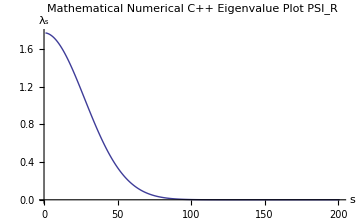
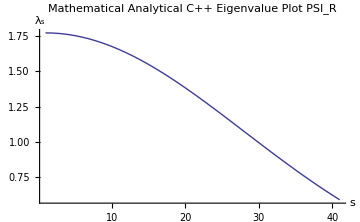

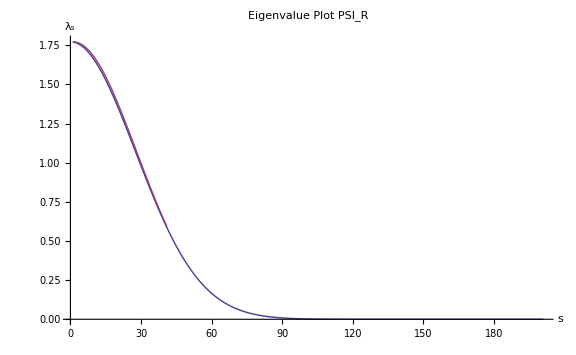

```mathematica
Subscript[Mλ, s]
Subscript[dataMAλ, s]
j=Table[{Subscript[Mλ, s][[i]],Subscript[dataMAλ, s][[i]],(Subscript[Mλ, s][[i]]/Subscript[dataMAλ, s][[i]])},{i,1,40}];
Grid[j]

Subscript[pMλ, s]=ListLinePlot[Subscript[Mλ, s],PlotStyle->{Thick},AxesLabel -> {s, Subscript[λ,s]},PlotLabel->"Mathematical Numerical C++ Eigenvalue Plot PSI_R",PlotRange->All,ImageSize->Medium];
Subscript[pdataMAλ, s]=ListLinePlot[Subscript[dataMAλ, s],PlotStyle->{Thick},AxesLabel -> {s, Subscript[λ,s]},PlotLabel->"Mathematical Analytical C++ Eigenvalue Plot PSI_R",PlotRange->All,ImageSize->Medium,PlotRange->All,AxesOrigin->{0,0}];

{Subscript[pMλ, s],Subscript[pdataMAλ, s]}
Subscript[EvalPlotλ, s]=ListLinePlot[{Subscript[Mλ, s],Subscript[dataMAλ, s]},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {s, Subscript[λ,s]},PlotLabel->"Eigenvalue Plot PSI_R",ImageSize->Large,LegendPosition->{0.5,0},PlotLegend->{"Numerical C++","Analytical C++","Numerical Mathematica","Analytical Mathematica"},LegendShadow->None,LegendBorder->None]
```

Numerical Calculation of Eigenfunctions (Mathematica)

ρ Eigenvalues

{0.80975,0.169,0.03527,0.00736,0.00154,0.00032,0.00007,0.00001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.80975,0.169,0.03527,0.00736,0.00154,0.00032,0.00007,0.00001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

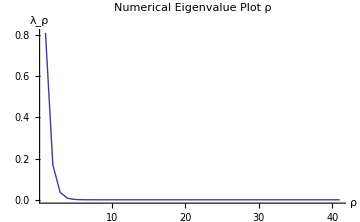

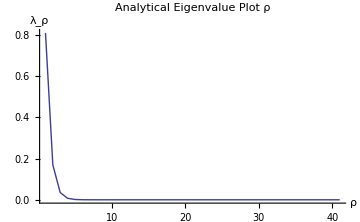

```mathematica
Subscript[Tλ, ρ] = Flatten[Import["./logs/TROE_eval.log","Table"]]
Subscript[aTλ, ρ] = Flatten[Import["./logs/LAMBDA_ROE.log","Table"]]

Subscript[pTλ, ρ]=ListLinePlot[Subscript[Tλ, ρ],PlotStyle->{Thick},AxesLabel -> {ρ, Subscript[λ,ρ]},PlotLabel->"Numerical Eigenvalue Plot ρ",PlotRange->All,ImageSize->Medium]
Subscript[paTλ, ρ]=ListLinePlot[Subscript[aTλ, ρ],PlotStyle->{Thick},PlotRange->All,AxesLabel -> {ρ, Subscript[λ,ρ]},PlotLabel->"Analytical Eigenvalue Plot ρ",ImageSize->Medium]
```

λ Eigenvalues

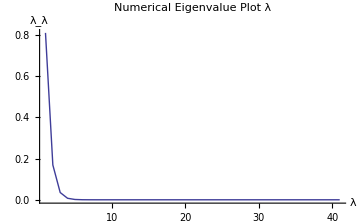

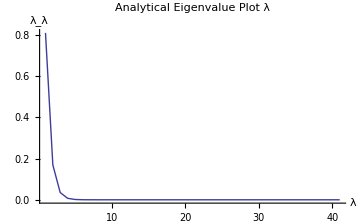

```mathematica
Subscript[Tλ, λ] = Flatten[Import["./logs/TLAMBDA_eval.log","Table"]];
Subscript[aTλ, λ] = Flatten[Import["./logs/LAMBDA_LAMBDA.log","Table"]];

Subscript[pTλ, λ]=ListLinePlot[Subscript[Tλ, λ],PlotStyle->{Thick},AxesLabel -> {λ, Subscript[λ,λ]},PlotLabel->"Numerical Eigenvalue Plot λ",PlotRange->All,ImageSize->Medium]
Subscript[paTλ, λ]=ListLinePlot[Subscript[aTλ, λ],PlotStyle->{Thick},PlotRange->All,AxesLabel -> {λ, Subscript[λ,λ]},PlotLabel->"Analytical Eigenvalue Plot λ",ImageSize->Medium]
```